Import data

```mathematica
data=ResourceData["Mass Shootings in America"]
```

Dataset[<>]

```mathematica
GeoHistogram[data[All,"Position"],"AdministrativeDivision1",ImageSize->Full]
```

-Graphics-

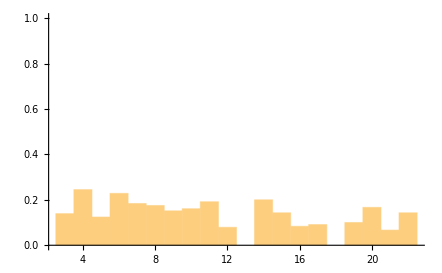

```mathematica
Histogram[data[All,"Total Number of Victims"],{1},"HF"]
```

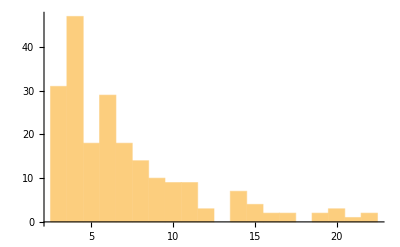

```mathematica
Histogram[data[All,"Total Number of Victims"],{1}]
```

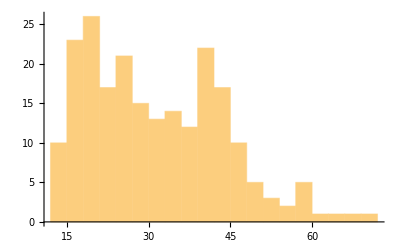

```mathematica
Histogram[Normal[data[All,"Average Shooter Age"]],{3}]
```

```mathematica
WolframAlpha["Average human age",{{"Result",1},"ComputableData"}]
```

66 yr

```mathematica
cts=Counts[data[All,"Shooter Race"]]
```

Dataset[<>]

```mathematica
Keys[cts]
```

Dataset[<>]

```mathematica
Counts[data[All,"Shooter Race"]];
PieChart[%,ChartLegends->Normal[Keys[%]],ChartStyle->"DarkRainbow"]
```

-Graphics-

```mathematica
PieChart[Normal[Counts[data[All,"Type of Gun – General"]]],ChartLegends->Keys[Normal[Counts[data[All,"Type of Gun – General"]]]],ChartStyle->"DarkRainbow"]
```

-Graphics-